# Magnetogenesis

## Parameters

Ratio of the eigenvalues of kinetic mixing

```mathematica
r  =  0.00147;
r  =  0.2;
r  =  0.15;
r  =  0.25;
r  =  0.19626156828141247;
```

The initial value of the initial rescaled conformal time

```mathematica
Subscript[y, in]  =  -10.0;
```

The final value of the rescaled conformal time

```mathematica
Subscript[y, right]  =  -10^-8;
```

```mathematica
(r - 1/r)^2/(4 (Subscript[y, in])^2)
 Abs[  (r - 1/r)/(2 (Subscript[y, in])^2)√(r^2  + 1/r^2  + 3)  ]
```

0.06

0.131909

## Definitions

A shorthand for the identity matrix

```mathematica
II  =  ({{1, 0}, {0, 1}});
```

The Hubble constant during inflation (GeV)  — not currently used

```mathematica
H  =  10^13;
```

The co-moving momentum as the function of the final conformal time (in the units of the Hubble constant)

```mathematica
k[y_]  =  - y;
```

The scale factor of the universe at the end of inflation, is normalized to be one

```mathematica
a  =  1.0;
```

The variable that enters the cosine / sine in the mass matrix

```mathematica
ζ̂  =  ( r + 1/r ) Log [ Subscript[y, in]/y];
```

The rescaled mass matrix

```mathematica
Q  = ( 1  -  1/y^2 ( r - 1/r )^2/4) II  -  0 1/y^2 (r - 1/r)/2 √(r^2 + 1/r^2 + 3)  ({{Cos[ζ̂], Sin[ζ̂]}, {Sin[ζ̂], - Cos[ζ̂]}});
```

The initial value of the function

```mathematica
Subscript[Ψ, in]   = II;
```

## Equations

Evolution equation

```mathematica
evolution  =  {     Ψ''[y]    +    Q . Ψ[y]    ==    0,
                                Ψ[Subscript[y, in]]  ==    Subscript[Ψ, in],
                                Ψ'[Subscript[y, in]]  ==  - ⅈ  Subscript[Ψ, in]                   };
```

## Solution

Solving the differential equation

```mathematica
solution = NDSolve[    evolution,    Ψ,    { y, Subscript[y, in], Subscript[y, right]},    MaxSteps->Infinity    ]
```

{{Ψ→InterpolatingFunction[{{-10.,-1.×10^-8}},<>]}}

The value where to plot starting from

```mathematica
Subscript[y, left]  =   4 Subscript[y, right];
```

```mathematica
Plot[    {  Abs[    (  Ψ[y] /. solution  )  [[1,1,1]]    ] },    {  y,  Subscript[y, left],  Subscript[y, right]  }    ]
```

-Graphics-

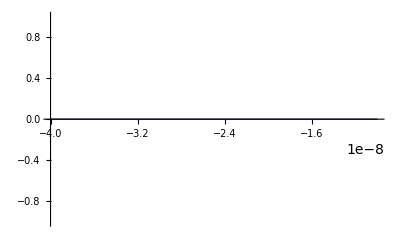

```mathematica
Plot[    {  Abs[    (  Ψ[y] /. solution  )  [[1,1,2]]    ] },    {  y,  Subscript[y, left],  Subscript[y, right]  }    ]
```

```mathematica
Plot[    {  Abs[    (  Ψ[y] /. solution  )  [[1,2,1]]    ] },    {  y,  Subscript[y, left],  Subscript[y, right]  }    ]
```

-Graphics-

```mathematica
Plot[    {  Abs[    (  Ψ[y] /. solution  )  [[1,2,2]]    ] },    {  y,  Subscript[y, left],  Subscript[y, right]  }    ]
```

-Graphics-

## Power Spectrum for the Magnetic Field

Parameter entering the diagonalization matrices (matrix Δ in my notations)

```mathematica
ρ  =  ArcSin[ 1/(√(r^2 + 1/r^2 + 3))];
```

Parameter of the rotation in the rotation matrix

```mathematica
s[y_]  =  1/2( r + 1/r ) Log[Subscript[y, in]/y]    -    1/2 ρ;
```

Rotation matrix which removes the one-derivative terms

```mathematica
R[y_]  =  ({{Cos[s[y]], -Sin[s[y]]}, {Sin[s[y]], Cos[s[y]]}});
```

Power Spectrum  —  as a function of the final conformal time

```mathematica
P[Ψ_, α_, y_] := 1/(2 π^2)(k[y]/a)^4 (    Re[  (  R[y]ᵀ . Ψ . Ψ† . Conjugate[R[y]]  )[[ α, α ]]  ]    )
```

We denote the solution itself with the letter Ξ

```mathematica
Ξ[y_]  :=  Evaluate[  Ψ[y]  /.  solution  ][[1]];
```

Calculate the Power Spectrum

InterpolatingFunction::dmval: Input value {18.4204} lies outside the range of data in the interpolating function. Extrapolation will be used.

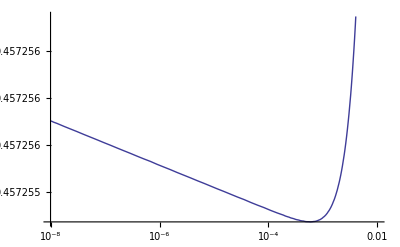

```mathematica
LogLogPlot[    {  P[  Ξ[(-x)],  1,  (-x)  ]  },  {  x,  -Subscript[y, right],  0.01  }    ]
```

Fit a linear function

```mathematica
NN  =  1000;
yy[p_]  :=  -  10^(Log10[  -Subscript[y, right]  ] p  / NN);
fitdata  =  Table[  {  Log10[  -yy[p]  ],  Log10[   P[  Ξ[yy[p]],  1,  yy[p] ]  ]  },  {  p,  0,  NN  }  ]  //  N;
fit  =  Fit[  fitdata, {  1,  x  },  x  ]
```

-0.323565+0.00300909 x

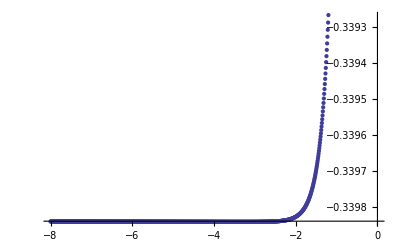

```mathematica
ListPlot[fitdata]
```